```mathematica
<<peeters`;
peeters`setGitDir["../project/figures/phy452-basicstatmech"]

fs=Style[#,FontSize->14]&;
```

/Users/pjoot/project/figures/phy452-basicstatmech

```mathematica
Clear[rho]
rho[tau_, mu_] = E^(mu/tau) (tau)^(-3/2) ;
Manipulate[
Plot[
rho[tau, mu], 
{tau, r, 10}, 
(*PlotRange->Full,*)
PlotStyle->Thick,
AxesLabel -> {Text["k_BT"]//fs, Subscript[ρ, Text["μ = "<>ToString[mu]]] / (h/Sqrt[ Text["(2 π m)"]])^3 // fs}
],
{{r, 0.2},0.01,2},
{mu,0.1,5}
]
```

```mathematica
lecture16Fig6 = DynamicModule[{mu=0.1,r=0.2},Plot[rho[tau,mu],{tau,r,10},
PlotStyle->{Thick,Black},
AxesLabel->{
MaTeX["k_{\\mathrm{B}} T"],
MaTeX["\\frac{1}{h^3} {\\left( 2 \\pi m \\right)}^{3/2} \\rho_{\\mu = 0.1}"]
(*fs[Text["\!\(\*SubscriptBox[\"k\", StyleBox[\"B\",FontWeight->\"Plain\"]]\)T"]],fs[Subscript[ρ, Text["μ = "<>ToString[mu]]]/(h/(√Text["(2 π m)"]))^3]*)
}]]
```

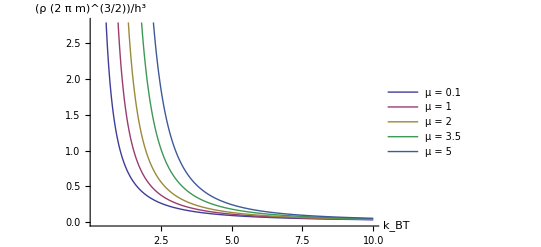

```mathematica
(* weird.  If this is moved into the cell above the placed legends don't work? *)

Plot[
Evaluate[Map[
rho[tau, #] &, {0.1, 1, 2, 3.5, 5}]], 
{tau, 0.2, 10}, 
AxesLabel -> {Text["k_BT"], ρ / (h/Sqrt[ Text["(2 π m)"]])^3},
PlotLegends->Placed[Map[Text[ "μ = "  <> ToString[#]]&, {0.1, 1, 2, 3.5, 5}], {Right,Top}]
]
```

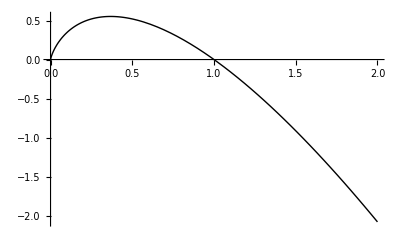

```mathematica
lecture16TLogTPlotFig7 =Plot[ 
- (3 tau/2) Log[tau], 
{tau, 0, 2},
PlotStyle->{Thick,Black},
AxesLabel->{
(*Subscript[k, B] T //fs,
 - 3 Subscript[k, B] T Log[Subscript[k, B] T]/2 //fs*)
MaTeX["k_{\\mathrm{B}} T"],
MaTeX["-\\frac{3}{2} k_{\\mathrm{B}} T \\log\\left(k_{\\mathrm{B}} T \\right)"]
}]
```

```mathematica
peeters`exportForLatex["lecture16Fig6",lecture16Fig6]
```

{lecture16Fig6.eps,lecture16Fig6pn.png}

```mathematica
peeters`exportForLatex["lecture16TLogTPlotFig7",lecture16TLogTPlotFig7]
```

{lecture16TLogTPlotFig7.eps,lecture16TLogTPlotFig7pn.png}